## For Problem Set 16 — SOLUTION — Was originally accidentally numbered 15)

## Exercises to go Along with Chapter 13

## 1. A Slightly Different Metropolis Procedure

Recall steps 5-8 of the procedure we used to generate the representative iPhone sales:

5. Draw a random number uniformly distributed between 0 and 1.
6. If the random number is less than the appropriate ratio, your position is the new quarter.
7. If the random number is greater than the appropriate ratio, your position is unchanged.
8. Either way, the computer reports a position (that is either the new or unchanged position).

My formula for the “appropriate ratio” was:

rBrian=(P(possible new position))/(P(current position)+P(possible new position))

I hope I convinced everyone that not only does it work, but then I spoke about “ergodicity” and why this specific choice of ratios works.

But now, let’s look at Donovan and Mickey’s appropriate ratio! It is:

rDonovanAndMickey=the minimum of((P(possible new position))/(P(current position)),1)

Let’s apply my formula and their formula to a terribly simple parent distribution:

```mathematica
unitSalesByFiscalHalfInMillions = {
{"H1", 75},
{"H2", 175}
};
annualUnitSales = Total[unitSalesByFiscalHalfInMillions][[2]];
normalizedUnitSales = N[unitSalesByFiscalHalfInMillions[[All,2]]/= annualUnitSales]
```

{0.3,0.7}

Above is the normalized distribution.

Now we need to compute the ratios. Here are the “appropriate ratios” done the way I showed you:

```mathematica
rBrian[n_,m_]:=Round[normalizedUnitSales[[m]]/(normalizedUnitSales[[m]]+normalizedUnitSales[[n]]),0.01];
rDonovanAndMickey[n_,m_]:=Round[Min[normalizedUnitSales[[m]]/normalizedUnitSales[[n]],1],0.01];
brianRatios={
{"1->2", rBrian[1,2]},
{"2->1", rBrian[2,1]}
};
donovanAndMickeyRatios={
{"1->2", "___1.0___"},
{"2->1", "__ 0.43___"}
};
TableForm[brianRatios]
```

1->2 | 0.7
2->1 | 0.3

You know my “appropriate ratios” work.

Fill in Donovan and Mickey’s “appropriate ratios” using their procedure. Round to two decimal places.

```mathematica
TableForm[donovanAndMickeyRatios]
```

1->2 | ___1.0___
2->1 | __ 0.43___

## 2. Applying the Slightly Different Procedure

(a) Write down the day of the month of your birthday:

(b) Below is a place you can make your Fiscal Half 1 (H1) and Fiscal Half 2 (H2) tallies. If your answer to (a) was odd, put the first tally in the H1 column. If your answer to (a) is even, but the first tally in the H2 column.

PLACE FOR TALLIES/NOTES
















(c) Since there are only two columns, you don’t need to do a coin flip to decide whether you go left or right! Either direction leads to the other column. You just need a random number between 0 and 1.

On the facing page is a table of 31 random numbers. Starting on the row that is your birthday, run the procedure 19 times and make 19 more tallies. Don’t use my appropriate ratios. Use the Donovan and Mickey ratios you filled in in Problem 1.

```mathematica
smallIterations=31;
randomReals=Round[RandomReal[{0,1},smallIterations],0.01];
rounds=Range[1,smallIterations];

TableForm[Transpose[{rounds,randomReals}]]
```

1 | 0.66
2 | 0.32
3 | 0.07
4 | 0.51
5 | 0.47
6 | 0.69
7 | 0.98
8 | 0.73
9 | 0.11
10 | 0.38
11 | 0.63
12 | 0.87
13 | 0.87
14 | 0.43
15 | 0.6
16 | 0.35
17 | 0.68
18 | 0.41
19 | 0.2
20 | 0.08
21 | 0.16
22 | 0.78
23 | 0.66
24 | 0.51
25 | 0.12
26 | 0.95
27 | 0.69
28 | 0.26
29 | 0.5
30 | 0.51
31 | 0.58

## 3. Comparing with Expectations

You ended up with 20 tallies total. From the parent distribution, if there are 20 tallies, you expect 20*0.3=6 in H1 and 20*0.7=14 in H2. What is the square root of 6? This is the expected standard deviation for H1. Is your H1 within or near 1 standard deviation of 6? E.g., near the range 3 to 9? It is a random process, so it doesn’t have to be, but it usually is.

Sqrt(6) is 2.45, so it would be very common to be off by ±3 or ±4 in the H1 tallies.  Sqrt(14) is 3.74 so it would be very common to be off by ±4 or in the H2 tallies.

## 4. Summary

In one sentence, what is the qualitative and quantitative difference between Donovan and Mickey’s “appropriate ratios” and the ones I showed you?

Qualitatively theirs are both larger, and  quantitatively, the ratio of the ratios is still 3:7 which is why the Principle of Detailed Balance still works with their ratios.

In the meantime, I let Mathematica off the leash to run the procedure 100,000 times.

```mathematica
position=RandomInteger[{1,2}];
accumulator = ConstantArray[0,2];
iterations = 100000;
randomNumbers=RandomReal[1,iterations];
accumulate[z_]:=(
newPosition=3 - position;
ratio=Min[normalizedUnitSales[[newPosition]]/normalizedUnitSales[[position]],1];
position = If[RandomReal[]<ratio,newPosition,position];
accumulator[[position]]+=1;
)
Map[accumulate,randomNumbers];
expected=normalizedUnitSales*iterations;
```

The representative sample matches the parent distribution so well I cannot tell the difference.

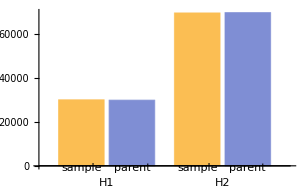

```mathematica
BarChart[Transpose[{accumulator,expected}],ChartLabels->{unitSalesByFiscalHalfInMillions[[All,1]],{"sample","parent"}}]
```